# Project Euler Problem 86

For a cuboid with sides a,b,c, there are three potentially optimal paths from one corner to the another, with lengths (a+b)^2+c^2, (a+c)^2+b^2, and a^2+(b+c)^2.

### naive solution: way too slow

```mathematica
integerPathCount[m_, M_] := Module[{cnt = 0},
	Do[
		If[IntegerQ[Min[Sqrt[{(x+y)^2 + z^2, x^2 + (y+z)^2, (x+z)^2 + y^2}]]], ++cnt],
		{x, m, M}, {y, x}, {z, y}
	];
	cnt
]
integerPathCount[M_] := integerPathCount[1, M]
```

```mathematica
slowPythagoreanCuboids[M_] := If[Length[#]==0, #, Sort[First[#]]]& @ Last[Reap[
	Do[
		If[IntegerQ[Min[Sqrt[{(x+y)^2 + z^2, x^2 + (y+z)^2, (x+z)^2 + y^2}]]], Sow[Sort[{x,y,z}]]],
		{x, 1, M}, {y, x}, {z, y}
	]
]]
```

```mathematica
integerPathCount[99]
```

1975

```mathematica
integerPathCount[100]
```

2060

```mathematica
integerPathCount[150]
```

4918

```mathematica
integerPathCount[200]
```

9034

```mathematica
integerPathCount[201,250]
```

5342

```mathematica
timings=Table[{M,First[Timing[integerPathCount[M]]]},{M,10,150,10}]
```

{{10,0.},{20,0.046875},{30,0.125},{40,0.3125},{50,0.609375},{60,1.0625},{70,1.75},{80,2.67188},{90,3.92188},{100,5.59375},{110,7.51563},{120,11.8906},{130,14.4375},{140,18.7188},{150,22.8594}}

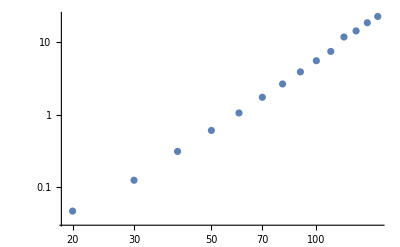

```mathematica
ListLogLogPlot[timings]
```

```mathematica
cnt = 0; Do[++cnt, {x,1000}, {y,x}, {z,y}] // Timing
```

{34.4375,Null}

### counting Pythogorean triples only

#### 1. Generate Pythagorean triples

```mathematica
pythagoreanTriples[M_] := If[Length[#] > 0, First[#], #]& @
	Last[Reap[Do[If[IntegerQ[Sqrt[a^2 + b^2]], Sow[{a, b}]], {a, 1, M}, {b, 1, a}]]]
```

#### 2. Generate the corresponding cuboid shapes for which the shortest path is the Pythagorean one

```mathematica
cuboidMinPathLengthSquared[a_, b_, c_] := Min[(a+b)^2 + c^2, (a+c)^2 + b^2, a^2 + (b+c)^2]
cuboidMinPathLength[a_, b_, c_] := Sqrt[cuboidMinPathLengthSquared[a, b, c]]
```

```mathematica
validCuboids[{x_, y_}] := With[
	{vals = Last[Reap[Module[{b, c, hsq = x^2 + y^2},
		c = y;
		Do[b = x - a; If[hsq == cuboidMinPathLengthSquared[a, b, c], Sow[Sort[{a, b, c}]]], {a, x/2}];
		c = x;
		Do[b = y - a; If[hsq == cuboidMinPathLengthSquared[a, b, c], Sow[Sort[{a, b, c}]]], {a, y/2}]
	]]]},
	If[Length[vals] == 0, vals, Union[First[vals]]]
]
```

```mathematica
pythagoreanCuboids[M_] := Select[Union[Join @@ (validCuboids /@ pythagoreanTriples[2M])], Last[#] ≤ M &]
```

```mathematica
M=2000;
res = Transpose[{#[[1]], Accumulate[#[[2]]]}] & @ Transpose[Sort[Tally[pythagoreanCuboids[M][[All, -1]]]]]
```

{{3,2},{4,3},{6,6},{8,10},{9,14},{12,25},{15,35},{16,43},{18,50},{20,67},{21,85},{24,113},{27,123},{28,139},{30,158},{32,173},{33,191},{35,197},{36,230},{39,244},{40,286},{42,321},{44,337},{45,379},{48,456},{51,474},{52,493},{54,512},{55,536},{56,589},{57,609},{60,729},{63,789},{64,818},{65,848},{66,882},{68,907},{69,931},{70,943},{72,1057},{75,1103},{76,1131},{77,1149},{78,1176},{80,1279},{81,1307},{84,1447},{85,1467},{87,1497},{88,1572},{90,1655},{91,1685},{92,1719},{93,1751},{95,1763},{96,1915},{99,1975},{100,2060},{102,2095},{104,2169},{105,2347},{108,2446},{110,2494},{111,2532},{112,2645},{114,2684},{116,2727},{117,2789},{119,2849},{120,3204},{123,3246},{124,3292},{126,3411},{128,3468},{129,3512},{130,3571},{132,3755},{133,3811},{135,3935},{136,3995},{138,4042},{140,4293},{141,4341},{143,4353},{144,4652},{147,4772},{148,4827},{150,4918},{152,4985},{153,5089},{154,5125},{156,5334},{159,5388},{160,5638},{161,5680},{162,5735},{164,5796},{165,6020},{168,6433},{170,6472},{171,6600},{172,6664},{174,6723},{175,6785},{176,6963},{177,7023},{180,7478},{182,7538},{183,7600},{184,7681},{186,7744},{187,7786},{188,7856},{189,8054},{190,8077},{192,8378},{195,8598},{196,8710},{198,8828},{200,9034},{201,9102},{203,9108},{204,9373},{207,9539},{208,9739},{209,9799},{210,10153},{212,10232},{213,10304},{216,10645},{219,10719},{220,11012},{221,11042},{222,11117},{224,11445},{225,11741},{228,12016},{231,12374},{232,12476},{234,12599},{236,12687},{237,12767},{238,12886},{240,13837},{243,13919},{244,14010},{245,14052},{246,14135},{247,14183},{248,14292},{249,14376},{252,15000},{253,15102},{255,15330},{256,15443},{258,15530},{260,15902},{261,16062},{264,16604},{266,16715},{267,16805},{268,16905},{270,17152},{272,17384},{273,17764},{275,18010},{276,18293},{279,18447},{280,19187},{282,19282},{284,19388},{285,19628},{286,19652},{288,20336},{291,20434},{292,20543},{294,20782},{296,20912},{297,21234},{299,21324},{300,21928},{303,22030},{304,22312},{306,22519},{308,22895},{309,22999},{312,23579},{315,24277},{316,24395},{318,24502},{319,24642},{320,25140},{321,25248},{322,25331},{323,25349},{324,25646},{325,25906},{327,26016},{328,26160},{330,26606},{332,26730},{333,26854},{336,28068},{339,28182},{340,28642},{341,28774},{342,29029},{344,29180},{345,29464},{348,29783},{350,29906},{351,30230},{352,30652},{354,30771},{356,30904},{357,31410},{360,32984},{363,33162},{364,33554},{366,33677},{368,33975},{369,34099},{372,34440},{374,34524},{375,34750},{376,34915},{377,35083},{378,35477},{380,35975},{381,36103},{384,36702},{385,37136},{387,37266},{388,37411},{390,37849},{391,37909},{392,38274},{393,38406},{396,39293},{399,39803},{400,40432},{402,40567},{403,40765},{404,40916},{405,41286},{406,41297},{407,41393},{408,42081},{411,42219},{412,42373},{414,42703},{416,43145},{417,43285},{418,43405},{420,45234},{423,45376},{424,45562},{425,45742},{426,45885},{428,46045},{429,46571},{432,47564},{435,47980},{436,48143},{437,48185},{438,48332},{440,49314},{441,49728},{442,49788},{444,50195},{447,50345},{448,51000},{450,51590},{451,51652},{452,51821},{453,51973},{455,52597},{456,53351},{459,53771},{460,54376},{462,55090},{464,55370},{465,55834},{468,56798},{471,56956},{472,57163},{473,57205},{474,57364},{475,57486},{476,58041},{477,58201},{480,60249},{481,60431},{483,60969},{484,61150},{486,61313},{488,61527},{489,61691},{490,61775},{492,62226},{493,62364},{494,62460},{495,63352},{496,63618},{498,63785},{500,64210},{501,64378},{504,66404},{506,66608},{507,66778},{508,66968},{510,67422},{512,67647},{513,68121},{516,68594},{519,68768},{520,69857},{522,70175},{524,70371},{525,71393},{527,71561},{528,73199},{531,73377},{532,73984},{533,74140},{534,74319},{536,74554},{537,74734},{539,74860},{540,76450},{543,76632},{544,77112},{546,77871},{548,78076},{549,78260},{550,78752},{551,78872},{552,79746},{555,80350},{556,80558},{558,80864},{559,81004},{560,82656},{561,83256},{564,83773},{567,84363},{568,84612},{570,85090},{572,85786},{573,85978},{575,86002},{576,87473},{579,87667},{580,88370},{582,88565},{584,88821},{585,89891},{588,90871},{589,91021},{591,91219},{592,91479},{594,92120},{595,92886},{596,93109},{597,93309},{598,93489},{600,95506},{603,95708},{604,95934},{605,96198},{606,96401},{608,97017},{609,97627},{611,97729},{612,98823},{615,99445},{616,100953},{618,101160},{620,101877},{621,102421},{624,104209},{627,104877},{628,105112},{629,105382},{630,106775},{632,107052},{633,107264},{636,107847},{637,108137},{638,108416},{639,108630},{640,109623},{642,109838},{644,110537},{645,111165},{646,111201},{648,112223},{650,112742},{651,113400},{652,113644},{654,113863},{656,114151},{657,114371},{660,116988},{663,117664},{664,117955},{665,118639},{666,118885},{667,118963},{668,119213},{669,119437},{672,122265},{675,123175},{676,123428},{678,123655},{680,124750},{681,124978},{682,125241},{684,126366},{687,126596},{688,126898},{689,126928},{690,127495},{692,127754},{693,128982},{696,130114},{697,130462},{699,130696},{700,132288},{702,132935},{703,133187},{704,134283},{705,134917},{708,135566},{711,135804},{712,136116},{713,136224},{714,137234},{715,137928},{716,138196},{717,138436},{720,142351},{723,142593},{724,142864},{725,142918},{726,143272},{728,144818},{729,145062},{731,145404},{732,146075},{735,147501},{736,148232},{738,148479},{740,149214},{741,149896},{744,151070},{747,151320},{748,152096},{750,152547},{752,152877},{753,153129},{754,153465},{756,155680},{759,156496},{760,157645},{762,157900},{764,158186},{765,159696},{768,160891},{770,161758},{771,162016},{772,162305},{774,162564},{775,162648},{776,162988},{777,163850},{779,164180},{780,167234},{782,167354},{783,167858},{784,168640},{786,168903},{788,169198},{789,169462},{792,172319},{795,172947},{796,173245},{798,174263},{799,174583},{800,176247},{801,176515},{804,177252},{805,177770},{806,178166},{807,178436},{808,178790},{810,179529},{812,180336},{813,180608},{814,180799},{816,183004},{817,183376},{819,184772},{820,185499},{822,185774},{824,186135},{825,187741},{828,189072},{831,189350},{832,190638},{833,191358},{834,191637},{836,192426},{837,192942},{840,198796},{843,199078},{844,199394},{845,199772},{846,200055},{847,200253},{848,200625},{849,200909},{850,201268},{851,201478},{852,202259},{855,204007},{856,204382},{858,205430},{860,206161},{861,207169},{864,209652},{867,209942},{868,210820},{870,211651},{872,212033},{873,212325},{874,212409},{875,212715},{876,213518},{879,213812},{880,216274},{882,217101},{884,218136},{885,218740},{888,220016},{891,220976},{892,221310},{893,221742},{894,222041},{896,223349},{897,224167},{899,224197},{900,226994},{901,227266},{902,227389},{903,228473},{904,228869},{906,229172},{908,229512},{909,229816},{910,231062},{912,233512},{915,234104},{916,234447},{918,235286},{920,236723},{921,237031},{924,240499},{925,240685},{927,240995},{928,241846},{930,242773},{931,243581},{932,243930},{933,244242},{935,245322},{936,248528},{939,248842},{940,249641},{942,249956},{943,250244},{944,250658},{945,252966},{946,253049},{948,253918},{950,254161},{951,254479},{952,256177},{954,256496},{956,256854},{957,257800},{960,262290},{962,262653},{963,262975},{964,263336},{966,264410},{968,265225},{969,266243},{972,267134},{975,268792},{976,269220},{978,269547},{980,271301},{981,271629},{984,272953},{986,273229},{987,274471},{988,275541},{989,275871},{990,277652},{992,278535},{993,278867},{996,279780},{999,280308},{1000,281334},{1001,281982},{1002,282317},{1003,282523},{1004,282899},{1005,283503},{1007,283899},{1008,289170},{1011,289508},{1012,290332},{1014,290671},{1015,290967},{1016,291412},{1017,291752},{1020,295518},{1023,296442},{1024,296891},{1025,297155},{1026,298102},{1028,298487},{1029,299321},{1032,300663},{1035,302685},{1036,303727},{1037,303907},{1038,304254},{1040,307272},{1041,307620},{1044,309120},{1045,310378},{1047,310728},{1048,311187},{1050,313228},{1052,313622},{1053,314592},{1054,314928},{1056,318820},{1059,319174},{1060,320075},{1062,320430},{1064,322236},{1065,322876},{1066,323187},{1068,324166},{1071,326332},{1072,326802},{1073,326934},{1074,327293},{1075,327599},{1076,328002},{1077,328362},{1078,328614},{1080,333947},{1081,334367},{1083,334729},{1084,335135},{1085,335387},{1086,335750},{1088,337077},{1089,337717},{1092,341668},{1095,342326},{1096,342806},{1098,343173},{1100,345214},{1101,345582},{1102,345822},{1104,348472},{1105,349486},{1107,350094},{1108,350509},{1110,351715},{1112,352202},{1113,353626},{1116,355204},{1118,355483},{1119,355857},{1120,360471},{1121,360813},{1122,362011},{1124,362432},{1125,363904},{1127,364660},{1128,366026},{1131,367078},{1132,367502},{1134,368680},{1136,369178},{1137,369558},{1139,369648},{1140,373707},{1143,374089},{1144,376582},{1146,376965},{1147,377067},{1148,378129},{1149,378513},{1150,378561},{1152,381500},{1155,385842},{1156,386275},{1158,386662},{1159,386982},{1160,388812},{1161,389480},{1164,390547},{1167,390937},{1168,391449},{1170,393586},{1172,394025},{1173,395171},{1175,395567},{1176,398500},{1178,398800},{1179,399194},{1180,400197},{1182,400592},{1183,400982},{1184,402057},{1185,402769},{1188,406132},{1189,406342},{1190,407872},{1191,408270},{1192,408792},{1194,409191},{1196,410295},{1197,412759},{1200,418383},{1203,418785},{1204,419851},{1206,420254},{1207,420274},{1208,420803},{1209,421941},{1210,422469},{1212,423580},{1215,424688},{1216,426251},{1218,427469},{1219,428039},{1220,429076},{1221,430026},{1222,430229},{1224,433946},{1225,434818},{1227,435228},{1228,435688},{1230,436930},{1232,440226},{1233,440638},{1235,441844},{1236,442977},{1239,444461},{1240,446393},{1242,447479},{1244,447945},{1245,448693},{1247,448945},{1248,453447},{1251,453865},{1252,454334},{1254,455668},{1256,456218},{1257,456638},{1258,457178},{1260,465269},{1263,465691},{1264,466245},{1265,467931},{1266,468354},{1268,468829},{1269,469623},{1271,469803},{1272,471235},{1273,471477},{1274,472056},{1275,473934},{1276,475147},{1278,475574},{1280,477557},{1281,479057},{1284,480234},{1287,482176},{1288,484162},{1290,485416},{1292,486946},{1293,487378},{1295,487636},{1296,490610},{1299,491044},{1300,493518},{1302,494833},{1304,495404},{1305,497708},{1308,498907},{1309,500157},{1311,501565},{1312,502740},{1314,503179},{1316,504241},{1317,504681},{1320,512984},{1323,514776},{1324,515272},{1325,515818},{1326,517168},{1328,517750},{1329,518194},{1330,519560},{1332,521348},{1333,521570},{1334,521726},{1335,522528},{1336,523113},{1338,523560},{1340,524699},{1341,525147},{1344,531090},{1347,531540},{1348,532045},{1349,532225},{1350,534043},{1352,534993},{1353,535983},{1356,537226},{1357,537846},{1359,538300},{1360,542038},{1362,542493},{1363,542835},{1364,544109},{1365,548965},{1368,552911},{1371,553369},{1372,554153},{1374,554612},{1375,555842},{1376,557025},{1377,558283},{1378,558342},{1380,562806},{1383,563268},{1384,563874},{1386,566328},{1387,566474},{1388,566994},{1389,567458},{1392,570676},{1394,571372},{1395,573758},{1396,574281},{1398,574748},{1400,579193},{1401,579661},{1403,580267},{1404,583777},{1406,584281},{1407,585817},{1408,588007},{1410,589273},{1412,589802},{1413,590274},{1416,591868},{1419,592872},{1420,594079},{1421,594505},{1422,594980},{1424,595604},{1425,597760},{1426,597976},{1428,603173},{1430,604559},{1431,605557},{1432,606184},{1434,606663},{1435,607023},{1436,607561},{1437,608041},{1440,617308},{1443,618372},{1444,618913},{1445,619237},{1446,619720},{1448,620354},{1449,623404},{1450,623512},{1452,625531},{1455,626405},{1456,629961},{1457,630273},{1458,630760},{1460,632001},{1461,632489},{1462,633172},{1463,634612},{1464,636260},{1467,636750},{1468,637300},{1470,640149},{1472,641857},{1473,642349},{1475,643063},{1476,645094},{1479,646442},{1480,648656},{1482,650019},{1484,651045},{1485,655015},{1488,658334},{1491,659884},{1492,660443},{1494,660942},{1495,662632},{1496,665557},{1497,666057},{1500,669073},{1501,669105},{1503,669607},{1504,670794},{1505,671208},{1506,671711},{1508,673030},{1509,673534},{1512,680321},{1515,681231},{1516,681799},{1517,681877},{1518,683507},{1519,683867},{1520,687896},{1521,688690},{1524,690087},{1525,690839},{1527,691349},{1528,692018},{1530,695035},{1532,695609},{1533,697163},{1536,699550},{1537,700042},{1539,701462},{1540,706896},{1541,707448},{1542,707963},{1544,708639},{1545,709567},{1547,711055},{1548,713236},{1550,713404},{1551,714438},{1552,715118},{1554,716841},{1556,717424},{1557,717944},{1558,718604},{1560,727894},{1563,728416},{1564,730206},{1566,731212},{1568,733995},{1569,734519},{1572,735960},{1573,736092},{1575,741352},{1576,742042},{1578,742569},{1580,743912},{1581,745354},{1584,752823},{1587,753353},{1588,753948},{1590,755202},{1591,755322},{1592,756019},{1593,757239},{1595,759177},{1596,764556},{1598,765195},{1599,766235},{1600,769760},{1602,770295},{1604,770896},{1605,771860},{1608,773670},{1610,774705},{1611,775243},{1612,776781},{1614,777320},{1615,777960},{1616,778668},{1617,781490},{1620,786258},{1623,786800},{1624,789023},{1625,790319},{1626,790862},{1628,792295},{1629,792839},{1632,798382},{1633,798888},{1634,799632},{1635,800614},{1636,801227},{1638,804018},{1640,806400},{1641,806948},{1643,807410},{1644,808917},{1645,809445},{1647,810743},{1648,811465},{1650,814675},{1652,815629},{1653,817143},{1656,821858},{1659,823412},{1660,824823},{1662,825378},{1664,827952},{1665,830498},{1666,831936},{1668,833465},{1671,834023},{1672,837170},{1674,838200},{1675,838910},{1676,839538},{1677,840598},{1679,841078},{1680,856818},{1683,859356},{1684,859987},{1686,860550},{1688,861289},{1689,861853},{1690,862608},{1692,864909},{1694,865305},{1695,866323},{1696,867486},{1698,868053},{1700,871547},{1701,873313},{1702,873733},{1704,875651},{1705,877567},{1707,878137},{1708,879113},{1710,882607},{1711,883267},{1712,884017},{1713,884589},{1715,884883},{1716,891286},{1719,891860},{1720,894348},{1722,896363},{1724,897009},{1725,899641},{1728,905066},{1729,906688},{1731,907266},{1732,907915},{1734,908494},{1736,910960},{1737,911540},{1739,911750},{1740,916661},{1743,918205},{1744,918969},{1746,919552},{1748,921703},{1749,922983},{1750,923594},{1752,925566},{1755,930344},{1756,931002},{1758,931589},{1760,937715},{1761,938303},{1763,938345},{1764,943439},{1767,945051},{1768,948263},{1769,948983},{1770,950189},{1771,952191},{1772,952855},{1773,953447},{1775,954119},{1776,957826},{1779,958420},{1780,959933},{1782,961850},{1784,962631},{1785,968349},{1786,969212},{1788,970851},{1791,971449},{1792,974063},{1794,975698},{1796,976371},{1797,976971},{1798,977031},{1800,986995},{1802,987538},{1803,988140},{1804,989659},{1805,989869},{1806,992036},{1808,992828},{1809,994302},{1812,995963},{1813,996221},{1815,998665},{1816,999460},{1817,999850},{1818,1000457},{1820,1006727},{1821,1007335},{1824,1013572},{1825,1014222},{1827,1017560},{1828,1018245},{1829,1018875},{1830,1020057},{1832,1020859},{1833,1021947},{1836,1026404},{1839,1027018},{1840,1031554},{1842,1032169},{1844,1032860},{1845,1035382},{1848,1046353},{1850,1046725},{1851,1047343},{1852,1048037},{1854,1048656},{1855,1049370},{1856,1051162},{1857,1051782},{1859,1051938},{1860,1057029},{1862,1058643},{1863,1060627},{1864,1061443},{1866,1062066},{1868,1062766},{1869,1064280},{1870,1066438},{1872,1074843},{1875,1075969},{1876,1077041},{1878,1077668},{1880,1080500},{1881,1083460},{1884,1085187},{1885,1087715},{1886,1088291},{1887,1090039},{1888,1091142},{1890,1095754},{1891,1096444},{1892,1098000},{1893,1098632},{1896,1100766},{1899,1101400},{1900,1105392},{1902,1106027},{1904,1110818},{1905,1111962},{1908,1114377},{1909,1114697},{1911,1117809},{1912,1118646},{1914,1120535},{1916,1121253},{1917,1122733},{1920,1131707},{1923,1132349},{1924,1134141},{1925,1138131},{1926,1138774},{1927,1138906},{1928,1139750},{1929,1140394},{1932,1146355},{1935,1148881},{1936,1150824},{1938,1152857},{1940,1154506},{1941,1155154},{1943,1156066},{1944,1159131},{1947,1160675},{1948,1161405},{1950,1164719},{1952,1165794},{1953,1169180},{1955,1170200},{1956,1171993},{1959,1172647},{1960,1178769},{1961,1179129},{1962,1179784},{1964,1180520},{1965,1181700},{1968,1185741},{1971,1187221},{1972,1189104},{1974,1191587},{1975,1192159},{1976,1195753},{1977,1196413},{1978,1197073},{1980,1209135},{1983,1209797},{1984,1211593},{1986,1212256},{1988,1213392},{1989,1216466},{1992,1218708},{1995,1224604},{1996,1225352},{1998,1226406},{2000,1229543}}

```mathematica
SelectFirst[res,Last[#]≥10^6&]
```

{1818,1000457}

```mathematica
Divide@@Reverse[N[Log[res[[-1]]]-Log[res[[-100]]]]]
```

2.12096

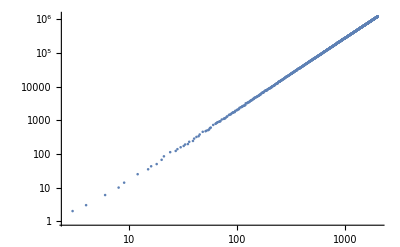

```mathematica
ListLogLogPlot[res]
```